```mathematica
(*Solution of A1*)
n=8;(*Consideration*)
(*a1*)
fact=1;(*Initialization*)
Do[fact=fact*i,{i,n}](*Do loop*)
fact(*Display result*)
```

40320

```mathematica
(*b*)
Divisors[n](*Shows the divisors*)
Total[Divisors[n]](*Shows the sum*)
```

{1,2,4,8}

15

```mathematica
(*c*)
pn={};(*Initialization*)
Do[If[PrimeQ[i],AppendTo[pn,i]],{i,n}](*Do loop to find and place prime upto n*)
pn(*Shows the result*)
```

{2,3,5,7}

```mathematica
(*d*)
∑_(i=1)^n i/(√i)//N(*Shows the Sum in Decimal form*)
```

16.306

```mathematica
(*e*)
binary = {1,0,1,0,1,0,1};(*Given*)
sum=0;(*Initialization*)
Do[sum=sum+binary[[i]]*2^(i-1),{i,Length[binary],1,-1}](*Do loop to transform binary into decimal*)
sum(*Shows result*)
```

85

```mathematica
(*Solution of A2*)
(*a*)
LogicalExpand[p∧(q∨r)]==LogicalExpand[(p∧q)∨(p∧r)]
LogicalExpand[¬(p∧q)]==LogicalExpand[¬p∨¬q]
```

True

True

```mathematica
(*b*)
∫_-5^5 ∫_(-√(25-x^2))^(√(25-x^2)) ∫_(-√(25-x^2-y^2))^(√(25-x^2-y^2)) ⅆzⅆyⅆx
```

(500 π)/3

```mathematica
(*c*)
∫_-6^6 ∫_(-(6-2 x^2))^(6-2 x^2) ∫_(-(6-2 x^2+4 y^2))^(6-2 x^2+4 y^2) ⅆzⅆyⅆx
```

-16327872/7

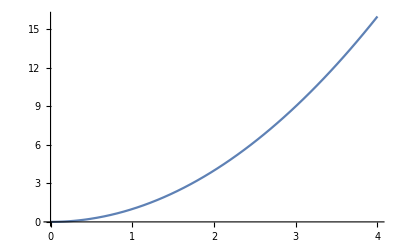

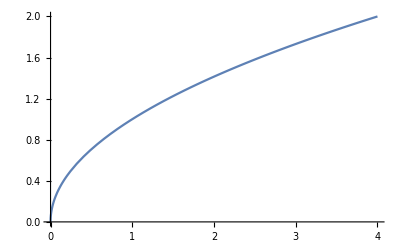

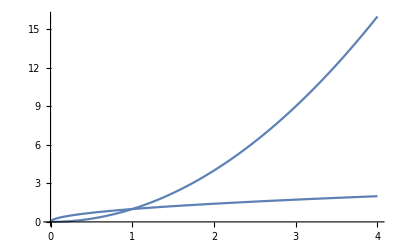

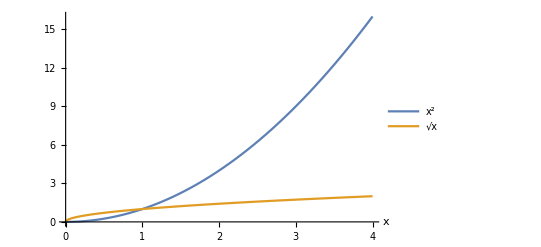

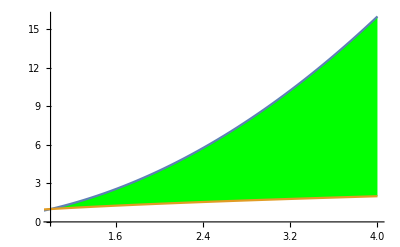

-1/3

49/3

```mathematica
(*Solution of B1*)
g1=Plot[x^2,{x,0,4}]
g2=Plot[√x,{x,0,4}]
Show[g1,g2]
Plot[{x^2,√x},{x,0,4},AxesLabel->Automatic,PlotLegends->"Expressions"]
p1=Plot[{x^2,√x},{x,0,1},Filling->{1->{{2},Yellow}}];
p2=Plot[{x^2,√x},{x,1,4},Filling->{1->{{2},Green}}];
Show[p2,p1]
∫_0^1 (x^2-√x)ⅆx
∫_1^4 (x^2-√x)ⅆx
```

```mathematica
(*Solution of B2*)
```

```mathematica
A=({{2, 2, 1}, {1, 3, 1}, {1, 2, 2}});
i=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
Det[A]
Length[RowReduce[A]]
Eigenvalues[A]
Eigenvectors[A]
Det[A-λ i]
5*i-11*A+7 MatrixPower[A,2]-MatrixPower[A,3]==({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})
```

5

3

{5,1,1}

{{1,1,1},{-1,0,1},{-2,1,0}}

5-11 λ+7 λ^2-λ^3

True